## MergeEdges-example.nb

Example Cellzilla2D notebook

GPL License applies.
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51d (10 June 2017)) loaded Sat 10 Jun 2017 19:28:22
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

```mathematica
w=TemplateRandom[7, {{0,0}, {10,0}, {11, 10},{5, 12},  {-1, 11}}];
```

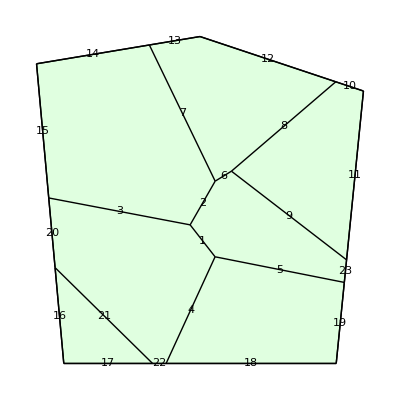

```mathematica
ShowTissue[w, "EdgeNumbers"-> True]
```

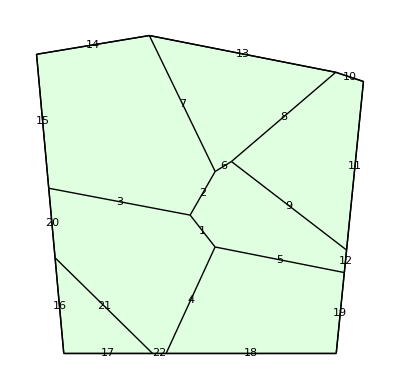

```mathematica
T=MergeEdges[w,12, 13];
ShowTissue[T, "EdgeNumbers"-> True]
```

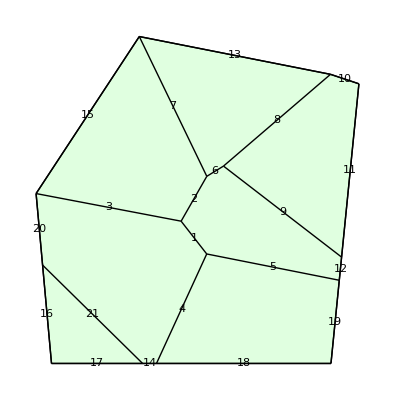

```mathematica
T1=MergeEdges[T,14,15];
ShowTissue[T1, "EdgeNumbers"-> True]
```

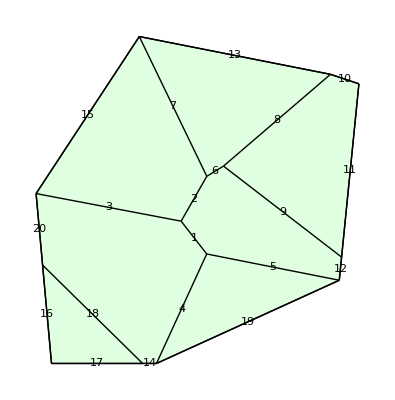

```mathematica
T2=MergeEdges[T1,18,19];
ShowTissue[T2, "EdgeNumbers"-> True]
```

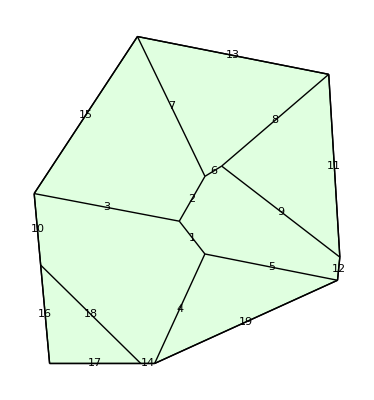

```mathematica
T3=MergeEdges[T2,10,11];
ShowTissue[T3, "EdgeNumbers"-> True]
```